```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0 && Element[k,Integers] && k>0
```

r>0&&m∈Integers&&n∈Integers&&s>0&&k∈Integers&&k>0

```mathematica
m=5;
```

```mathematica
f[r_,En_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}}-0*IdentityMatrix[2]*I*r^p;f[r,En]//MatrixForm
```

(4/r | ⅈ (En-r^4)
ⅈ (En-r^4) | -5/r)

```mathematica
En=.;n=.;p=4
```

4

```mathematica
fE=D[f[r,En],En]
```

{{0,ⅈ},{ⅈ,0}}

```mathematica
u={a[n]*x^(2*n),b[n]*x^(2*n+1)}*x^s
```

{x^(2 n+s) a[n],x^(1+2 n+s) b[n]}

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[(D[u,x]-r'[x]*f[r[x],En].u)*x^(-s+1)]]],{x^n,a[n],b[n]}];
g1//MatrixForm
```

(x^(2 n) ((-4+2 n+s) a[n]+(-ⅈ En x^2+ⅈ x^6) b[n])
x^(2 n) ((-ⅈ En x+ⅈ x^5) a[n]+(6 x+2 n x+s x) b[n]))

```mathematica
s=-1+m;
```

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,10}]/.x->0],{n2,0,10}];g2//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
a[0]=1; b[0]=ⅈ En a[0]/2/m;a[1]=ⅈ En b[0]/2;b[1]=-(ⅈ En^3)/(4 m)/2/ (1+m) ;a[2]=ⅈ En b[1]/4;
```

```mathematica
b[n_]:=Simplify[(-ⅈ a[n-2]+ⅈ En a[n])/(2 (n+m) )];
a[n_]:=Simplify[-ⅈ (b[n-3]-En b[n-1])/2/n]
```

```mathematica
b[4]
```

(ⅈ En^4 (-22464+En^5))/185794560

```mathematica
Un[En_,m_,nN_,x_]:=Module[{n,U},
U={1};AppendTo[U,-En^2/(4 m)];AppendTo[U,(En (4+En^3+8 m))/(32 m (1+m))];G={ⅈ En /2/m};

For[n=3,n<nN,n++,
AppendTo[U,-((-1+m+n) U[[-2+n]]+En ((3-2 m-2 n) U[[-1+n]]+En (-2+m+n)U[[n]]))/(4 n (-2+m+n) (-1+m+n))];
];
({1,ⅈ En /2/m*x}+Sum[{U[[n+1]]*x^(2*n),I*(En*U[[n+1]]-U[[n]])/2/(n+m)*x^(2*n+1)},{n,1,nN-1} ])*x^(-1+m)//N]
```

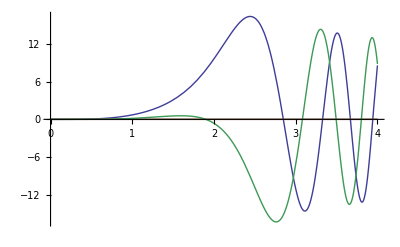

```mathematica
G={Re[#],Im[#]}&[Un[3,5,150,x]];Plot[G,{x,0,4},PlotRange->All]
```

```mathematica
U[En_,m_,g_,X_]:=Module[{n=10,U,G},
U=Un[En,m,n,X];G=-Un[En,m,n+1,X];
While[Sqrt[Abs[Conjugate[U-G].(U-G)]]>g,
n++;
U=G;G=-Un[En,m,n+1,X];

];
{Un[En,m,n,X],n}]
```

```mathematica
U[9,5,0.0001,1]
```

{{-0.0126898,0.+0.00407705 ⅈ},14}

```mathematica
Ener[Ene_]:=Module[{U1,U2,U1S,U2S,VV={{0,1},{-1,0}},En,Enn,NN,Erg,kE,k,n,m,r,h},
En=Ene;
Label[begin];
n=5000;
m=5;
r=7.2//N;h=-7.0/n;
k={1,-1};
kE={0,0};
Do[
k0=h*f[r,En].k;k1=h*f[r+h/2,En].(k+k0/2);k2=h*f[r+h/2,En].(k+k1/2);k3=h*f[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);

k0=h*(fE.k+f[r,En].kE);k1=h*(fE.k+f[r+h/2,En].(kE+k0/2));k2=h*(fE.k+f[r+h/2,En].(kE+k1/2));k3=h*(fE.k+f[r+h,En].(kE+k2));
kE+=1/6*(k0+2*k1+2*k2+k3);

r+=h;
,{n}];

NN=U[En,m,0.0001,r][[2]];

{U1,U2}=Un[En,m,NN,r];
{U1S,U2S}=D[Un[Enn,m,NN,r],Enn]/.Enn->En;

Erg=k[[1]]*U2-U1*k[[2]];

If[Abs[Erg/U2/k[[2]]]>0.001,
En-=Erg/(U2S k⟦1⟧-U1S k⟦2⟧+U2 kE⟦1⟧-U1 kE⟦2⟧);
Print[{En,Erg/U2/k[[2]]}];Goto[begin];
 ];
{En,Erg/U2/k[[2]]}
]
```

```mathematica
For[i=0,i<10,i+=0.1,Sepp=Ener[i];Print[{i,Sepp}];AppendTo[Energie,{i,Sepp}];]
```

```mathematica
Ener[24.236924123512843+0.7062238874780654 ⅈ]
```

{24.2369+0.706395 ⅈ,0.00716219+0.0160044 ⅈ}

{24.2369+0.70624 ⅈ,-0.00746584-0.014522 ⅈ}

{24.2369+0.70638 ⅈ,0.00722303+0.0122471 ⅈ}

{24.2369+0.706253 ⅈ,-0.00732641-0.0109237 ⅈ}

{24.2369+0.706367 ⅈ,0.00693458+0.00920459 ⅈ}

{24.2369+0.706265 ⅈ,-0.00687771-0.00806601 ⅈ}

{24.2369+0.706356 ⅈ,0.00642544+0.00677406 ⅈ}

{24.2369+0.706275 ⅈ,-0.00625369-0.00582549 ⅈ}

{24.2369+0.706347 ⅈ,0.00579245+0.00485995 ⅈ}

{24.2369+0.706283 ⅈ,-0.00554783-0.00409206 ⅈ}

{24.2369+0.70634 ⅈ,0.00510631+0.00337537 ⅈ}

{24.2369+0.70629 ⅈ,-0.00482361-0.00277015 ⅈ}

{24.2369+0.706333 ⅈ,0.00441676+0.00224297 ⅈ}

{24.2369+0.706296 ⅈ,-0.00412247-0.00177825 ⅈ}

{24.2369+0.706328 ⅈ,0.00375707+0.00139525 ⅈ}

{24.2369+0.7063 ⅈ,-0.00346992-0.00104786 ⅈ}

{24.2369+0.706324 ⅈ,0.00314793+0.000774337 ⅈ}

{24.2369+0.706304 ⅈ,-0.00288004-0.000522185 ⅈ}

{24.2369+0.706321 ⅈ,0.00260061+0.000331457 ⅈ}

{24.2369+0.706307 ⅈ,-0.00235896-0.00015467 ⅈ}

{24.2369+0.706319 ⅈ,0.00211965+0.000026144 ⅈ}

{24.2369+0.706309 ⅈ,-0.00190737+0.0000924182 ⅈ}

{24.2369+0.706317 ⅈ,0.00170489-0.000174675 ⅈ}

{24.2369+0.70631 ⅈ,-0.00152244+0.000249309 ⅈ}

{24.2369+0.706316 ⅈ,0.00135309-0.000297629 ⅈ}

{24.2369+0.706311 ⅈ,-0.00119918+0.000339948 ⅈ}

{24.2369+0.706315 ⅈ,0.00105913-0.000363853 ⅈ}

{24.2369+0.706312 ⅈ,-0.000931431+0.000383066 ⅈ}

{24.2369+0.706312 ⅈ,0.00081691-0.000389864 ⅈ}

```mathematica
Energie={{3.77486283903418+0.22786873407418717 ⅈ,
5.928479968617718+0.2815986526347655 ⅈ,
7.8813588488087065+0.30953294412328675 ⅈ,
7.881329304880588+0.3095336916562825 ⅈ,
9.71036454189739+0.3304415424573178 ⅈ,
11.458077781781169+0.3457848857997222 ⅈ,
13.139764183242892+0.3546744769440479 ⅈ,
13.139114444715846+0.3548172513559829 ⅈ,
14.76566063867228+0.3636637795053202 ⅈ,
16.34527139193304+0.3681521067888729 ⅈ,
17.892138695416435+0.3696213478944415 ⅈ,
19.40831608562361+0.37704222997528414 ⅈ,
20.886015743223094+0.38097023642873473 ⅈ,
22.34958939297449+0.38276309915136164 ⅈ,23.777494591007947+0.3872991704766671 ⅈ},{12.207301904640477+0.09130244038237889 ⅈ,13.879319291317909+0.10359131716054014 ⅈ,17.071331521063737+0.12274708920757649 ⅈ,18.607651751873114+0.1305970820854307 ⅈ,20.11139546248976+0.1375815129955693 ⅈ,21.586240037178456+0.14389862151162078 ⅈ,23.03567690195356+0.149533964468945 ⅈ,
24.236898126799336+0.7063122785768635 ⅈ,25.86917074582206+0.1600892949325245 ⅈ}};Energie//MatrixForm
```

({3.77486+0.227869 ⅈ,5.92848+0.281599 ⅈ,7.88136+0.309533 ⅈ,7.88133+0.309534 ⅈ,9.71036+0.330442 ⅈ,11.4581+0.345785 ⅈ,13.1398+0.354674 ⅈ,13.1391+0.354817 ⅈ,14.7657+0.363664 ⅈ,16.3453+0.368152 ⅈ,17.8921+0.369621 ⅈ,19.4083+0.377042 ⅈ,20.886+0.38097 ⅈ,22.3496+0.382763 ⅈ,23.7775+0.387299 ⅈ}
{12.2073+0.0913024 ⅈ,13.8793+0.103591 ⅈ,17.0713+0.122747 ⅈ,18.6077+0.130597 ⅈ,20.1114+0.137582 ⅈ,21.5862+0.143899 ⅈ,23.0357+0.149534 ⅈ,24.2369+0.706312 ⅈ,25.8692+0.160089 ⅈ})

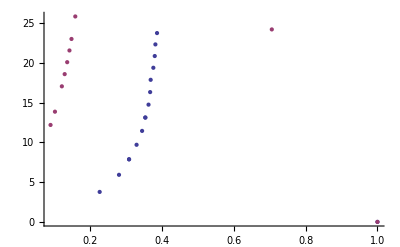

```mathematica
ListPlot[Table[Append[{Im[#],Re[#]}&/@Energie[[i]],{1,0}],{i,1,2}],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
:
```

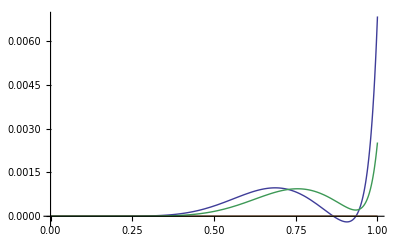

```mathematica
G={Re[#],Im[#]}&[Un[16,10,15,x]];Plot[G,{x,0,1},PlotRange->All]
```

27

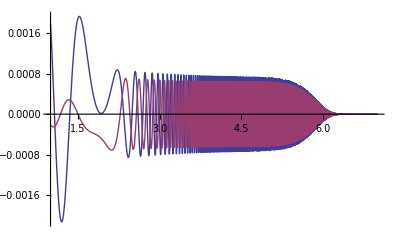

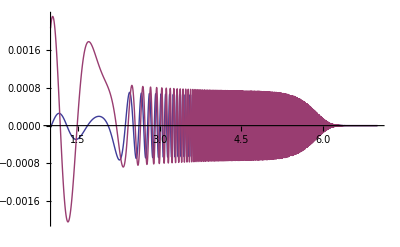

```mathematica
n=8000;S=1;h=6/n;ra=1;En=Energie[[17]];m=5;r=1;
U[En,m,10^-10,r][[2]]
k=U[En,m,10^-10,r][[1]];
kK={{r,k}};
Do[
k0=h*f[r,En].k;k1=h*f[r+h/2,En].(k+k0/2);k2=h*f[r+h/2,En].(k+k1/2);k3=h*f[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{n}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]
En=.;r=.;
```

```mathematica
U[En,m,10^-10,r][[1]]
```

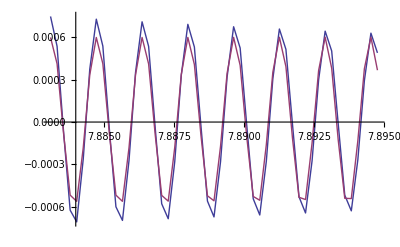

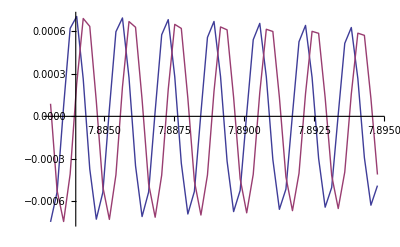

```mathematica
S=29500;n=50;ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],-0.0006*Sin[#[[1]]^5/5+1-#[[1]]*Re[Energie[[11]]]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->True]
```

```mathematica
Exp[I*Im[Energie[[1]]]*x]
```

ⅇ^(0.278733 ⅈ x)